```mathematica
Clear[J,ϵ,α];
$Assumptions=Element[{J,ϵ,α,ω,β,η,Ε},Reals]&&J>ϵ>0 && α>0&&ω>0 && β>0&&J>η>0 && J>Ε>0;
H0={{0,J,0},
{J,0,0},
{0,0,0}}; (*system hamiltonian in local site basis*)
H1={{0,0,ϵ},
{0,0,ϵ},
{ϵ,ϵ,Ε}};
H=H0+H1;
Slist={{{1,0,0},{0,0,0},{0,0,0}},
{{0,0,0},{0,1,0},{0,0,0}},
{{0,0,0},{0,0,0},{0,0,1}}};
n=3;
dens[x_]:=2*α*x*Exp[-x/ω];(* spectral density function for baths-assume all have same alpha,wc*)
eta[x_]:=1/(Exp[β*x]-1);(*the thermal factor*)

gammafunc[w_]:=Piecewise[{{(Pi/2)*(α/β),w==0},{(Pi/4)*dens[Abs[w]]*(eta[Abs[w]]+1),w>0},{(Pi/4)*dens[Abs[w]]*eta[Abs[w]],w<0}}];

(*diagonalise non perturbed hamiltonian*)
{evals,evecs}=Eigensystem[H0];
evals=evals[[{1,3,2}]]
evecs=Normalize/@evecs[[{1,3,2}]];
U=Transpose[evecs];

(*convert perturbation to unperturbed basis*)
H1eig=ConjugateTranspose[U].H1.U;
evecspert=Table[evecs[[k]]-Sum[If[j!=k,(H1eig[[j,k]]/(evals[[j]]-evals[[k]]))*evecs[[j]],0],{j,n}],{k,n}]; (*eigenvectors perturbed to 1st order*)
evecspert=Normalize/@evecspert;
U=Simplify[Transpose[Normalize/@evecspert]]; (*new cob matrix defining the energy basis*)

evalspert=Simplify[Table[evals[[k]]+H1eig[[k,k]],{k,n}]](*eigenvalues perturbed to 1st order*)
(*evalspert=Simplify[Table[evals[[k]]+H1eig[[k,k]]-Sum[If[j!=k,H1eig[[j,k]]*Conjugate[H1eig[[j,k]]]/(evals[[j]]-evals[[k]]),0],{j,n}],{k,n}]]*)

Seig=Simplify[Table[ConjugateTranspose[U].Slist[[k]].U,{k,n}]](*put coupling operators into energy basis*)

approx1[expr_]:=Module[{delta,kappa},Simplify[Normal[Series[expr/.{ϵ->delta J,η->kappa J},{delta,0,1},{kappa,0,1}]]/.{delta->ϵ/J,kappa->η/J}]];
(*approx2[expr_]:=Module[{delta,kappa},Simplify[Normal[Series[expr/.{ϵ->delta J,η->kappa J},{delta,0,2},{kappa,0,2}]]/.{delta->ϵ/J,kappa->η/J}]];*)
approx2[expr_]:=Module[{λ},Simplify[Normal[Series[expr/. {ϵ->λ ϵ,η->λ η},{λ,0,2}]]/. λ->1]];

(*simplevals= approx1/@evals;*)
simplevals=evalspert;
(*Seig=Table[Map[approx1,Seig[[k]],{2}],{k,n}];*)

R=ConstantArray[0,{n^2,n^2,n+1}];(*empty redfield tensor*)
idx[x_,y_]:=(x-1)*n+y; (*vectorization reindexing map*)
deltaE=Outer[Subtract,simplevals,simplevals]; (*matrix with energy differnces using approximate eigenvalues*)
gammaVals=Map[gammafunc,deltaE,{2}];
gammaValsConj=Conjugate[gammaVals];
Do[a=Quotient[ab-1,n]+1;
b=Mod[ab-1,n]+1;
R[[ab,ab,1]]=-I*deltaE[[a,b]];(*unitary part*)
R[[ab,idx[d,b],k+1]]-=Seig[[k,a,c]]*Seig[[k,c,d]]*gammaVals[[d,c]];(*term 1*)
R[[ab,idx[a,c],k+1]]-=Seig[[k,b,d]]*Seig[[k,d,c]]*gammaValsConj[[c,d]];(*term 2*)
R[[ab,idx[c,d],k+1]]+=Seig[[k,d,b]]*Seig[[k,a,c]]*gammaVals[[c,a]]; (*term 3*)
R[[ab,idx[c,d],k+1]]+=Seig[[k,c,a]]*Seig[[k,b,d]]*gammaValsConj[[d,b]], (*term 4*)
{ab,n^2},{c,n},{d,n},{k,n}];
R=Total[R,{3}];
Print["initial R built"]
COB={
{1,0,0,0,0,0,0,0,0},
{0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,0,0,1},
{0,1,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,0,1,0}};
Rprime=COB.R.Transpose[COB]; (*reorder so that we get the block form*)
Do[ If[(i>3 &&j<=3) || (i<=3 && j>3), Rprime[[i,j]]=0],{i,9},{j,9}];

popmat=Rprime[[1;;3,1;;3]];

Print["popmat built"]

popmatnew=popmat/.Exp[x_]:>Exp[Limit[x,ω->Infinity]];

Simplify[popmatnew]//MatrixForm;

popmat2=Map[approx2,popmatnew,{2}];


FullSimplify[popmat2]//MatrixForm

eigs=Eigenvalues[popmat2];
TableForm[eigs]
Print["evals to 2nd"]
list=FullSimplify[approx2/@eigs];
TableForm[list[[{2,3}]]]
```

{-J,0,J}

{-J,Ε,J}

{{{1/2,ϵ/(√2 √(J^2+2 ϵ^2)),-J/(2 √(J^2+2 ϵ^2))},{ϵ/(√2 √(J^2+2 ϵ^2)),ϵ^2/(J^2+2 ϵ^2),-(J ϵ)/(√2 (J^2+2 ϵ^2))},{-J/(2 √(J^2+2 ϵ^2)),-(J ϵ)/(√2 (J^2+2 ϵ^2)),1/(2+(4 ϵ^2)/J^2)}},{{1/2,-ϵ/(√2 √(J^2+2 ϵ^2)),J/(2 √(J^2+2 ϵ^2))},{-ϵ/(√2 √(J^2+2 ϵ^2)),ϵ^2/(J^2+2 ϵ^2),-(J ϵ)/(√2 (J^2+2 ϵ^2))},{J/(2 √(J^2+2 ϵ^2)),-(J ϵ)/(√2 (J^2+2 ϵ^2)),1/(2+(4 ϵ^2)/J^2)}},{{0,0,0},{0,J^2/(J^2+2 ϵ^2),(√2 J ϵ)/(J^2+2 ϵ^2)},{0,(√2 J ϵ)/(J^2+2 ϵ^2),(2 ϵ^2)/(J^2+2 ϵ^2)}}}

initial R built

popmat built

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

General::stop: Further output of Limit::alimv will be suppressed during this calculation.

((π α (-(ϵ^2 (J+Ε))/(-1+ⅇ^(β (J+Ε)))-1/2 J (J^2-2 ϵ^2) (-1+Coth[J β])))/J^2 | ((1+1/(-1+ⅇ^(β (J+Ε)))) π α ϵ^2 (J+Ε))/J^2 | (π α (J^2-2 ϵ^2) (1+Coth[J β]))/(2 J)
(π α ϵ^2 (J+Ε))/((-1+ⅇ^(β (J+Ε))) J^2) | (π α ϵ^2 (-(3 (J-Ε))/(-1+ⅇ^(β (J-Ε)))-(1+1/(-1+ⅇ^(β (J+Ε)))) (J+Ε)))/J^2 | (3 (1+1/(-1+ⅇ^(β (J-Ε)))) π α ϵ^2 (J-Ε))/J^2
(π α (J^2-2 ϵ^2) (-1+Coth[J β]))/(2 J) | (3 π α ϵ^2 (J-Ε))/((-1+ⅇ^(β (J-Ε))) J^2) | (π α (-3 (1+1/(-1+ⅇ^(β (J-Ε)))) ϵ^2 (J-Ε)-1/2 J^3 (1+Coth[J β])+J ϵ^2 (1+Coth[J β])))/J^2)

0
(π α (-J^3-2 ⅇ^(2 J β) J^3-ⅇ^(4 J β) J^3+ⅇ^(2 J β+β (J-Ε)) J^3+ⅇ^(β (J-Ε)) J^3+ⅇ^(β (J+Ε)) J^3+ⅇ^(2 J β+β (J+Ε)) J^3-2 J ϵ^2+12 ⅇ^(2 J β) J ϵ^2-2 ⅇ^(4 J β) J ϵ^2-4 ⅇ^(β (J-Ε)) J ϵ^2-4 ⅇ^(2 J β+β (J+Ε)) J ϵ^2+2 ϵ^2 Ε-4 ⅇ^(2 J β) ϵ^2 Ε+2 ⅇ^(4 J β) ϵ^2 Ε-4 ⅇ^(2 J β+β (J-Ε)) ϵ^2 Ε+4 ⅇ^(β (J-Ε)) ϵ^2 Ε-4 ⅇ^(β (J+Ε)) ϵ^2 Ε+4 ⅇ^(2 J β+β (J+Ε)) ϵ^2 Ε-√((J^3+2 ⅇ^(2 J β) J^3+ⅇ^(4 J β) J^3-ⅇ^(2 J β+β (J-Ε)) J^3-ⅇ^(β (J-Ε)) J^3-ⅇ^(β (J+Ε)) J^3-ⅇ^(2 J β+β (J+Ε)) J^3+2 J ϵ^2-12 ⅇ^(2 J β) J ϵ^2+2 ⅇ^(4 J β) J ϵ^2+4 ⅇ^(β (J-Ε)) J ϵ^2+4 ⅇ^(2 J β+β (J+Ε)) J ϵ^2-2 ϵ^2 Ε+4 ⅇ^(2 J β) ϵ^2 Ε-2 ⅇ^(4 J β) ϵ^2 Ε+4 ⅇ^(2 J β+β (J-Ε)) ϵ^2 Ε-4 ⅇ^(β (J-Ε)) ϵ^2 Ε+4 ⅇ^(β (J+Ε)) ϵ^2 Ε-4 ⅇ^(2 J β+β (J+Ε)) ϵ^2 Ε)^2-4 (3 J^4 ϵ^2-ⅇ^(2 J β) J^4 ϵ^2-3 ⅇ^(6 J β) J^4 ϵ^2+ⅇ^(8 J β) J^4 ϵ^2-5 ⅇ^(2 J β+β (J-Ε)) J^4 ϵ^2+5 ⅇ^(4 J β+β (J-Ε)) J^4 ϵ^2-3 ⅇ^(2 β (J-Ε)) J^4 ϵ^2+4 ⅇ^(2 β (2 J-Ε)) J^4 ϵ^2-ⅇ^(2 β (3 J-Ε)) J^4 ϵ^2-5 ⅇ^(β (J+Ε)) J^4 ϵ^2+2 ⅇ^(2 β (J+Ε)) J^4 ϵ^2-2 ⅇ^(2 β (3 J+Ε)) J^4 ϵ^2-ⅇ^(2 J β+β (J+Ε)) J^4 ϵ^2+6 ⅇ^(4 J β+β (J+Ε)) J^4 ϵ^2+7 ⅇ^(2 β (J-Ε)+β (J+Ε)) J^4 ϵ^2-7 ⅇ^(2 J β+2 β (J-Ε)+β (J+Ε)) J^4 ϵ^2+2 ⅇ^(β (J-Ε)+2 β (J+Ε)) J^4 ϵ^2-3 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) J^4 ϵ^2+ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) J^4 ϵ^2-3 J^2 ϵ^4-ⅇ^(2 J β) J^2 ϵ^4+3 ⅇ^(6 J β) J^2 ϵ^4+ⅇ^(8 J β) J^2 ϵ^4+10 ⅇ^(2 J β+β (J-Ε)) J^2 ϵ^4-10 ⅇ^(4 J β+β (J-Ε)) J^2 ϵ^4+3 ⅇ^(2 β (J-Ε)) J^2 ϵ^4-2 ⅇ^(2 β (2 J-Ε)) J^2 ϵ^4-ⅇ^(2 β (3 J-Ε)) J^2 ϵ^4+7 ⅇ^(β (J+Ε)) J^2 ϵ^4-4 ⅇ^(2 β (J+Ε)) J^2 ϵ^4+4 ⅇ^(2 β (3 J+Ε)) J^2 ϵ^4+8 ⅇ^(2 J β+β (J+Ε)) J^2 ϵ^4-15 ⅇ^(4 J β+β (J+Ε)) J^2 ϵ^4-14 ⅇ^(2 β (J-Ε)+β (J+Ε)) J^2 ϵ^4+14 ⅇ^(2 J β+2 β (J-Ε)+β (J+Ε)) J^2 ϵ^4-7 ⅇ^(β (J-Ε)+2 β (J+Ε)) J^2 ϵ^4+12 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) J^2 ϵ^4-5 ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) J^2 ϵ^4-3 J^3 ϵ^2 Ε-ⅇ^(2 J β) J^3 ϵ^2 Ε+3 ⅇ^(6 J β) J^3 ϵ^2 Ε+ⅇ^(8 J β) J^3 ϵ^2 Ε+ⅇ^(2 J β+β (J-Ε)) J^3 ϵ^2 Ε-ⅇ^(4 J β+β (J-Ε)) J^3 ϵ^2 Ε+3 ⅇ^(2 β (J-Ε)) J^3 ϵ^2 Ε-2 ⅇ^(2 β (2 J-Ε)) J^3 ϵ^2 Ε-ⅇ^(2 β (3 J-Ε)) J^3 ϵ^2 Ε+7 ⅇ^(β (J+Ε)) J^3 ϵ^2 Ε-4 ⅇ^(2 β (J+Ε)) J^3 ϵ^2 Ε+4 ⅇ^(2 β (3 J+Ε)) J^3 ϵ^2 Ε-ⅇ^(2 J β+β (J+Ε)) J^3 ϵ^2 Ε-6 ⅇ^(4 J β+β (J+Ε)) J^3 ϵ^2 Ε-5 ⅇ^(2 β (J-Ε)+β (J+Ε)) J^3 ϵ^2 Ε+5 ⅇ^(2 J β+2 β (J-Ε)+β (J+Ε)) J^3 ϵ^2 Ε+2 ⅇ^(β (J-Ε)+2 β (J+Ε)) J^3 ϵ^2 Ε+3 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) J^3 ϵ^2 Ε-5 ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) J^3 ϵ^2 Ε+6 J ϵ^4 Ε+2 ⅇ^(2 J β) J ϵ^4 Ε-6 ⅇ^(6 J β) J ϵ^4 Ε-2 ⅇ^(8 J β) J ϵ^4 Ε-2 ⅇ^(2 J β+β (J-Ε)) J ϵ^4 Ε+2 ⅇ^(4 J β+β (J-Ε)) J ϵ^4 Ε-6 ⅇ^(2 β (J-Ε)) J ϵ^4 Ε+4 ⅇ^(2 β (2 J-Ε)) J ϵ^4 Ε+2 ⅇ^(2 β (3 J-Ε)) J ϵ^4 Ε-14 ⅇ^(β (J+Ε)) J ϵ^4 Ε+8 ⅇ^(2 β (J+Ε)) J ϵ^4 Ε-8 ⅇ^(2 β (3 J+Ε)) J ϵ^4 Ε+2 ⅇ^(2 J β+β (J+Ε)) J ϵ^4 Ε+12 ⅇ^(4 J β+β (J+Ε)) J ϵ^4 Ε+10 ⅇ^(2 β (J-Ε)+β (J+Ε)) J ϵ^4 Ε-10 ⅇ^(2 J β+2 β (J-Ε)+β (J+Ε)) J ϵ^4 Ε-4 ⅇ^(β (J-Ε)+2 β (J+Ε)) J ϵ^4 Ε-6 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) J ϵ^4 Ε+10 ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) J ϵ^4 Ε-3 ϵ^4 Ε^2+3 ⅇ^(2 J β) ϵ^4 Ε^2+3 ⅇ^(6 J β) ϵ^4 Ε^2-3 ⅇ^(8 J β) ϵ^4 Ε^2+3 ⅇ^(2 β (J-Ε)) ϵ^4 Ε^2-6 ⅇ^(2 β (2 J-Ε)) ϵ^4 Ε^2+3 ⅇ^(2 β (3 J-Ε)) ϵ^4 Ε^2+3 ⅇ^(β (J+Ε)) ϵ^4 Ε^2-6 ⅇ^(2 J β+β (J+Ε)) ϵ^4 Ε^2+3 ⅇ^(4 J β+β (J+Ε)) ϵ^4 Ε^2+3 ⅇ^(β (J-Ε)+2 β (J+Ε)) ϵ^4 Ε^2-6 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) ϵ^4 Ε^2+3 ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) ϵ^4 Ε^2))))/(2 (-1+ⅇ^(2 J β)) (-1+ⅇ^(β (J-Ε))) (-1+ⅇ^(β (J+Ε))) J^2)
(π α (-J^3-2 ⅇ^(2 J β) J^3-ⅇ^(4 J β) J^3+ⅇ^(2 J β+β (J-Ε)) J^3+ⅇ^(β (J-Ε)) J^3+ⅇ^(β (J+Ε)) J^3+ⅇ^(2 J β+β (J+Ε)) J^3-2 J ϵ^2+12 ⅇ^(2 J β) J ϵ^2-2 ⅇ^(4 J β) J ϵ^2-4 ⅇ^(β (J-Ε)) J ϵ^2-4 ⅇ^(2 J β+β (J+Ε)) J ϵ^2+2 ϵ^2 Ε-4 ⅇ^(2 J β) ϵ^2 Ε+2 ⅇ^(4 J β) ϵ^2 Ε-4 ⅇ^(2 J β+β (J-Ε)) ϵ^2 Ε+4 ⅇ^(β (J-Ε)) ϵ^2 Ε-4 ⅇ^(β (J+Ε)) ϵ^2 Ε+4 ⅇ^(2 J β+β (J+Ε)) ϵ^2 Ε+√((J^3+2 ⅇ^(2 J β) J^3+ⅇ^(4 J β) J^3-ⅇ^(2 J β+β (J-Ε)) J^3-ⅇ^(β (J-Ε)) J^3-ⅇ^(β (J+Ε)) J^3-ⅇ^(2 J β+β (J+Ε)) J^3+2 J ϵ^2-12 ⅇ^(2 J β) J ϵ^2+2 ⅇ^(4 J β) J ϵ^2+4 ⅇ^(β (J-Ε)) J ϵ^2+4 ⅇ^(2 J β+β (J+Ε)) J ϵ^2-2 ϵ^2 Ε+4 ⅇ^(2 J β) ϵ^2 Ε-2 ⅇ^(4 J β) ϵ^2 Ε+4 ⅇ^(2 J β+β (J-Ε)) ϵ^2 Ε-4 ⅇ^(β (J-Ε)) ϵ^2 Ε+4 ⅇ^(β (J+Ε)) ϵ^2 Ε-4 ⅇ^(2 J β+β (J+Ε)) ϵ^2 Ε)^2-4 (3 J^4 ϵ^2-ⅇ^(2 J β) J^4 ϵ^2-3 ⅇ^(6 J β) J^4 ϵ^2+ⅇ^(8 J β) J^4 ϵ^2-5 ⅇ^(2 J β+β (J-Ε)) J^4 ϵ^2+5 ⅇ^(4 J β+β (J-Ε)) J^4 ϵ^2-3 ⅇ^(2 β (J-Ε)) J^4 ϵ^2+4 ⅇ^(2 β (2 J-Ε)) J^4 ϵ^2-ⅇ^(2 β (3 J-Ε)) J^4 ϵ^2-5 ⅇ^(β (J+Ε)) J^4 ϵ^2+2 ⅇ^(2 β (J+Ε)) J^4 ϵ^2-2 ⅇ^(2 β (3 J+Ε)) J^4 ϵ^2-ⅇ^(2 J β+β (J+Ε)) J^4 ϵ^2+6 ⅇ^(4 J β+β (J+Ε)) J^4 ϵ^2+7 ⅇ^(2 β (J-Ε)+β (J+Ε)) J^4 ϵ^2-7 ⅇ^(2 J β+2 β (J-Ε)+β (J+Ε)) J^4 ϵ^2+2 ⅇ^(β (J-Ε)+2 β (J+Ε)) J^4 ϵ^2-3 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) J^4 ϵ^2+ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) J^4 ϵ^2-3 J^2 ϵ^4-ⅇ^(2 J β) J^2 ϵ^4+3 ⅇ^(6 J β) J^2 ϵ^4+ⅇ^(8 J β) J^2 ϵ^4+10 ⅇ^(2 J β+β (J-Ε)) J^2 ϵ^4-10 ⅇ^(4 J β+β (J-Ε)) J^2 ϵ^4+3 ⅇ^(2 β (J-Ε)) J^2 ϵ^4-2 ⅇ^(2 β (2 J-Ε)) J^2 ϵ^4-ⅇ^(2 β (3 J-Ε)) J^2 ϵ^4+7 ⅇ^(β (J+Ε)) J^2 ϵ^4-4 ⅇ^(2 β (J+Ε)) J^2 ϵ^4+4 ⅇ^(2 β (3 J+Ε)) J^2 ϵ^4+8 ⅇ^(2 J β+β (J+Ε)) J^2 ϵ^4-15 ⅇ^(4 J β+β (J+Ε)) J^2 ϵ^4-14 ⅇ^(2 β (J-Ε)+β (J+Ε)) J^2 ϵ^4+14 ⅇ^(2 J β+2 β (J-Ε)+β (J+Ε)) J^2 ϵ^4-7 ⅇ^(β (J-Ε)+2 β (J+Ε)) J^2 ϵ^4+12 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) J^2 ϵ^4-5 ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) J^2 ϵ^4-3 J^3 ϵ^2 Ε-ⅇ^(2 J β) J^3 ϵ^2 Ε+3 ⅇ^(6 J β) J^3 ϵ^2 Ε+ⅇ^(8 J β) J^3 ϵ^2 Ε+ⅇ^(2 J β+β (J-Ε)) J^3 ϵ^2 Ε-ⅇ^(4 J β+β (J-Ε)) J^3 ϵ^2 Ε+3 ⅇ^(2 β (J-Ε)) J^3 ϵ^2 Ε-2 ⅇ^(2 β (2 J-Ε)) J^3 ϵ^2 Ε-ⅇ^(2 β (3 J-Ε)) J^3 ϵ^2 Ε+7 ⅇ^(β (J+Ε)) J^3 ϵ^2 Ε-4 ⅇ^(2 β (J+Ε)) J^3 ϵ^2 Ε+4 ⅇ^(2 β (3 J+Ε)) J^3 ϵ^2 Ε-ⅇ^(2 J β+β (J+Ε)) J^3 ϵ^2 Ε-6 ⅇ^(4 J β+β (J+Ε)) J^3 ϵ^2 Ε-5 ⅇ^(2 β (J-Ε)+β (J+Ε)) J^3 ϵ^2 Ε+5 ⅇ^(2 J β+2 β (J-Ε)+β (J+Ε)) J^3 ϵ^2 Ε+2 ⅇ^(β (J-Ε)+2 β (J+Ε)) J^3 ϵ^2 Ε+3 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) J^3 ϵ^2 Ε-5 ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) J^3 ϵ^2 Ε+6 J ϵ^4 Ε+2 ⅇ^(2 J β) J ϵ^4 Ε-6 ⅇ^(6 J β) J ϵ^4 Ε-2 ⅇ^(8 J β) J ϵ^4 Ε-2 ⅇ^(2 J β+β (J-Ε)) J ϵ^4 Ε+2 ⅇ^(4 J β+β (J-Ε)) J ϵ^4 Ε-6 ⅇ^(2 β (J-Ε)) J ϵ^4 Ε+4 ⅇ^(2 β (2 J-Ε)) J ϵ^4 Ε+2 ⅇ^(2 β (3 J-Ε)) J ϵ^4 Ε-14 ⅇ^(β (J+Ε)) J ϵ^4 Ε+8 ⅇ^(2 β (J+Ε)) J ϵ^4 Ε-8 ⅇ^(2 β (3 J+Ε)) J ϵ^4 Ε+2 ⅇ^(2 J β+β (J+Ε)) J ϵ^4 Ε+12 ⅇ^(4 J β+β (J+Ε)) J ϵ^4 Ε+10 ⅇ^(2 β (J-Ε)+β (J+Ε)) J ϵ^4 Ε-10 ⅇ^(2 J β+2 β (J-Ε)+β (J+Ε)) J ϵ^4 Ε-4 ⅇ^(β (J-Ε)+2 β (J+Ε)) J ϵ^4 Ε-6 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) J ϵ^4 Ε+10 ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) J ϵ^4 Ε-3 ϵ^4 Ε^2+3 ⅇ^(2 J β) ϵ^4 Ε^2+3 ⅇ^(6 J β) ϵ^4 Ε^2-3 ⅇ^(8 J β) ϵ^4 Ε^2+3 ⅇ^(2 β (J-Ε)) ϵ^4 Ε^2-6 ⅇ^(2 β (2 J-Ε)) ϵ^4 Ε^2+3 ⅇ^(2 β (3 J-Ε)) ϵ^4 Ε^2+3 ⅇ^(β (J+Ε)) ϵ^4 Ε^2-6 ⅇ^(2 J β+β (J+Ε)) ϵ^4 Ε^2+3 ⅇ^(4 J β+β (J+Ε)) ϵ^4 Ε^2+3 ⅇ^(β (J-Ε)+2 β (J+Ε)) ϵ^4 Ε^2-6 ⅇ^(2 J β+β (J-Ε)+2 β (J+Ε)) ϵ^4 Ε^2+3 ⅇ^(4 J β+β (J-Ε)+2 β (J+Ε)) ϵ^4 Ε^2))))/(2 (-1+ⅇ^(2 J β)) (-1+ⅇ^(β (J-Ε))) (-1+ⅇ^(β (J+Ε))) J^2)

evals to 2nd

Piecewise[{{-((ⅇ^(J β)+ⅇ^(β Ε)+ⅇ^(β (2 J+Ε))) π α ϵ^2 (-3 J+ⅇ^(2 J β) J+2 ⅇ^(β (J+Ε)) (J-2 Ε)+3 Ε+ⅇ^(2 J β) Ε))/((1+ⅇ^(2 J β)) (ⅇ^(J β)-ⅇ^(β Ε)) (-1+ⅇ^(β (J+Ε))) J^2), Cosh[J β]<Cosh[β Ε]}, {1/((-1+ⅇ^(4 J β)) (ⅇ^(J β)-ⅇ^(β Ε)) (-1+ⅇ^(β (J+Ε))) J^2)π α (ⅇ^(β (J+2 Ε)) J (J^2-2 ϵ^2)+2 ⅇ^(3 J β+2 β Ε) J (J^2-2 ϵ^2)+ⅇ^(5 J β+2 β Ε) J (J^2-2 ϵ^2)+ⅇ^(5 J β) (J^3+J ϵ^2-3 ϵ^2 Ε)-ⅇ^(β (6 J+Ε)) (J^3+J ϵ^2-3 ϵ^2 Ε)+2 ⅇ^(3 J β) (J^3-4 J ϵ^2+ϵ^2 Ε)-3 ⅇ^(β (4 J+Ε)) (J^3-3 J ϵ^2+ϵ^2 Ε)+ⅇ^(J β) (J^3-J ϵ^2+ϵ^2 Ε)-ⅇ^(β Ε) (J^3-J ϵ^2+ϵ^2 Ε)+ⅇ^(β (2 J+Ε)) (-3 J^3+7 J ϵ^2+ϵ^2 Ε)), True}}]
Piecewise[{{-((ⅇ^(J β)+ⅇ^(β Ε)+ⅇ^(β (2 J+Ε))) π α ϵ^2 (-3 J+ⅇ^(2 J β) J+2 ⅇ^(β (J+Ε)) (J-2 Ε)+3 Ε+ⅇ^(2 J β) Ε))/((1+ⅇ^(2 J β)) (ⅇ^(J β)-ⅇ^(β Ε)) (-1+ⅇ^(β (J+Ε))) J^2), Cosh[J β]≥Cosh[β Ε]}, {1/((-1+ⅇ^(4 J β)) (ⅇ^(J β)-ⅇ^(β Ε)) (-1+ⅇ^(β (J+Ε))) J^2)π α (ⅇ^(β (J+2 Ε)) J (J^2-2 ϵ^2)+2 ⅇ^(3 J β+2 β Ε) J (J^2-2 ϵ^2)+ⅇ^(5 J β+2 β Ε) J (J^2-2 ϵ^2)+ⅇ^(5 J β) (J^3+J ϵ^2-3 ϵ^2 Ε)-ⅇ^(β (6 J+Ε)) (J^3+J ϵ^2-3 ϵ^2 Ε)+2 ⅇ^(3 J β) (J^3-4 J ϵ^2+ϵ^2 Ε)-3 ⅇ^(β (4 J+Ε)) (J^3-3 J ϵ^2+ϵ^2 Ε)+ⅇ^(J β) (J^3-J ϵ^2+ϵ^2 Ε)-ⅇ^(β Ε) (J^3-J ϵ^2+ϵ^2 Ε)+ⅇ^(β (2 J+Ε)) (-3 J^3+7 J ϵ^2+ϵ^2 Ε)), True}}]

1/1000000

0.1

1/100

1/10000

(0.000314159 (-0.000999999 ⅇ^(β/100)+0.000999999 ⅇ^(0.1 β)+0.000999998 ⅇ^(0.12 β)-0.00299999 ⅇ^(0.21 β)+0.00199999 ⅇ^(0.3 β)+0.002 ⅇ^(0.32 β)-0.00299999 ⅇ^(0.41 β)+0.001 ⅇ^(0.5 β)+0.000999998 ⅇ^(0.52 β)-0.001 ⅇ^(0.61 β)))/((-ⅇ^(β/100)+ⅇ^(0.1 β)) (-1+ⅇ^(0.11 β)) (-1+ⅇ^(0.4 β)))

-(3.14159×10^-12 (-0.27+0.16 ⅇ^(0.11 β)+0.11 ⅇ^(0.2 β)) (ⅇ^(β/100)+ⅇ^(0.1 β)+ⅇ^(0.21 β)))/((-ⅇ^(β/100)+ⅇ^(0.1 β)) (-1+ⅇ^(0.11 β)) (1+ⅇ^(0.2 β)))

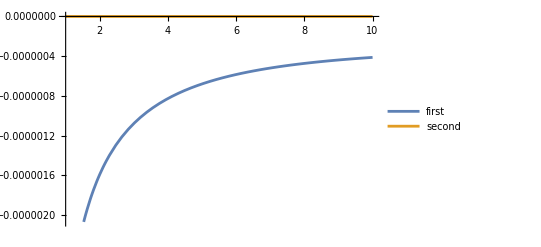

```mathematica
α=10^(-6)
J=0.1
Ε=10^(-2)
ϵ=10^(-4)

first=1/((-1+ⅇ^(4 J β)) (ⅇ^(J β)-ⅇ^(β Ε)) (-1+ⅇ^(β (J+Ε))) J^2)π α (ⅇ^(β (J+2 Ε)) J (J^2-2 ϵ^2)+2 ⅇ^(3 J β+2 β Ε) J (J^2-2 ϵ^2)+ⅇ^(5 J β+2 β Ε) J (J^2-2 ϵ^2)+ⅇ^(5 J β) (J^3+J ϵ^2-3 ϵ^2 Ε)-ⅇ^(β (6 J+Ε)) (J^3+J ϵ^2-3 ϵ^2 Ε)+2 ⅇ^(3 J β) (J^3-4 J ϵ^2+ϵ^2 Ε)-3 ⅇ^(β (4 J+Ε)) (J^3-3 J ϵ^2+ϵ^2 Ε)+ⅇ^(J β) (J^3-J ϵ^2+ϵ^2 Ε)-ⅇ^(β Ε) (J^3-J ϵ^2+ϵ^2 Ε)+ⅇ^(β (2 J+Ε)) (-3 J^3+7 J ϵ^2+ϵ^2 Ε))
second=-((ⅇ^(J β)+ⅇ^(β Ε)+ⅇ^(β (2 J+Ε))) π α ϵ^2 (-3 J+ⅇ^(2 J β) J+2 ⅇ^(β (J+Ε)) (J-2 Ε)+3 Ε+ⅇ^(2 J β) Ε))/((1+ⅇ^(2 J β)) (ⅇ^(J β)-ⅇ^(β Ε)) (-1+ⅇ^(β (J+Ε))) J^2)
Plot[{first,second},{β,1,10},PlotLegends->{"first","second"}]
```